```mathematica
<<MaTeX`
```

### 2D Zernike moments

```mathematica
(* plotting staff, auxilary functions *)
(* convert expression (fucntion) from polar coordinates to cartesian *)
r2c[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>x/r}/.r^n_:>(x^2+y^2)^(n/2)] 
(*  *)
zPlot[e_]:=With[{f= r2c[e]},DensityPlot[  f,{x,-1,1},{y,-1,1},RegionFunction:>(#1^2+#2^2≤1&), PlotPoints->12,Frame->False, ImageSize->120, ColorFunction->"BlueGreenYellow"]]
```

```mathematica
{maxX, maxY} = {101,101};
{x0, y0} = {1/maxX, 1/maxY};


(* radial polynomials *)
(* n ≥ m , n - m is even *)
R[n_, m_, r_]:=Sum[((-1)^k(n-k)!)/(k! ((n+m)/2 - k)! ((n-m)/2 - k)!)r^(n - 2 k),{k,0, (n - m)/2,1}]

(* Zernike polynomials *)
Z[n_, m_,r_, θ_]:=ZernikeR[Abs@n,Abs@m,r]*If[m ≥0, Cos[m θ], Sin[Abs@m θ]] (*R[n, m, r]*) 
(* Zernike moments for given 2D img *)
A[n_, m_, IMG_] := (m+1)/π Sum[IMG⟦x + Quotient[Length@IMG,2]+1, y + Quotient[Length@IMG,2] + 1⟧ r2c[Z[n,m,r,θ]],{x, -Quotient[Length@IMG,2], Quotient[Length@IMG,2]}, {y, -Quotient[Length@IMG,2], Quotient[Length@IMG,2]}]
```

```mathematica
LablAlig={-1.2, 1};
Grid[
{{Overlay[{zPlot[Z[0,0,r,θ]], MaTeX["Z^{"<>ToString[0]<>"}_{"<> ToString[0]<>"}", Magnification->1.5]}, Alignment->LablAlig]},

Flatten@Table[Overlay[{zPlot[Z[1,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[1]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-1, 1}}],

Table[Overlay[{zPlot[Z[2,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[2]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-2, 0, 2}}],

Table[Overlay[{zPlot[Z[3,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[3]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-3, -1, 1, 3}}],

Table[Overlay[{zPlot[Z[4,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[4]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-4, -2, 0, 2, 4}}]
}]
```

-Graphics--Graphics- |  |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

#### Test on the 2D points cloud

Test of orthogonality

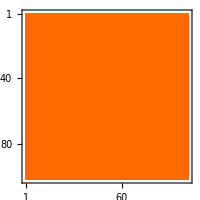

```mathematica
test2DList = Table[r2c[Z[0,0,r, θ]](*If[Mod[i+j, 2] == 0, 1,0]*), {x,-Quotient[maxX,2], Quotient[maxY,2]}, {y,-Quotient[maxX,2], Quotient[maxY,2]}];
(*test2DList⟦4, 4⟧ = 8/ 29;
test2DList⟦7, 7⟧ = 8 / 29;
test2DList⟦4, 7⟧ = 1 ;
test2DList⟦7, 4⟧ = 1;*)
MatrixPlot[test2DList, ImageSize->200]
```

```mathematica
Length@test2DList
```

101

```mathematica
Table[{mn⟦1⟧, mn⟦2⟧, A[mn⟦1⟧,mn⟦2⟧,test2DList]//N},{mn, {{0,0}, {-1, 1}, {1, 1}, {-2, 2}, {0, 2}, {2, 2}, {-3, 3}, {-1, 3}, {1, 3}, {3, 3}, {-4, 4},{-2, 4}, {0, 4}, {2, 4}, {4, 4}}}]//TableForm
```

0 | 0 | 3247.08
-1 | 1 | 0.
1 | 1 | 0.
-2 | 2 | 0.
0 | 2 | 0.
2 | 2 | 0.
-3 | 3 | 0.
-1 | 3 | 0.
1 | 3 | 0.
3 | 3 | 0.
-4 | 4 | -2.81577×10^10
-2 | 4 | 0.
0 | 4 | 0.
2 | 4 | 0.
4 | 4 | -2.81577×10^10